```mathematica
ClearAll[r, x, y, z];
r0 = 1;
r[θ_, r0_] := r0 Sin[θ]^2;
x[θ_, φ_, r0_] := r[θ, r0] Sin[θ] Cos[φ];
y[θ_,  φ_, r0_] := r[θ, r0] Sin[θ] Sin[φ];
z[θ_,  φ_, r0_] := r[θ, r0] Cos[θ];
```

```mathematica
φ = π/4;
r0 = 1/4;
img = ParametricPlot3D[{
x[θ, φ, r0], y[θ, φ, r0], z[θ, φ, r0]
}, {θ, 0, 2π}, {φ, 0, 2π} ,
 PlotStyle->{Opacity[0.5], RGBColor[0, 0.7, 0]}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
path = "D:\\Kami\\git_folder\\notes_4sem\\field_theory\\homework\\figures\\"
Export[path<>"T13.pdf", img]
```

D:\Kami\git_folder\notes_4sem\field_theory\homework\figures\

D:\Kami\git_folder\notes_4sem\field_theory\homework\figures\T13.pdf

## ТеорВер

### Четвертая задача

```mathematica
f = c Exp[-y^2+4 y - 10];
F = Integrate[f, {y, -∞, +∞}]
```

(c √π)/ⅇ^6

```mathematica
Solve[F == 1, c]⟦1⟧
```

{c→ⅇ^6/(√π)}

```mathematica
-y^2+4 y - 10 
y^2-4 y + 10 
Expand[-(y-2)^2-6]
```

-10+4 y-y^2

10-4 y+y^2

-10+4 y-y^2

```mathematica
f2 = ⅇ^6/(√π)Exp[-y^2+4 y - 10];
Integrate[f2, y]
Integrate[y f2, y]
Integrate[y^2 f2, y]
Integrate[f2, {y, -∞, +∞}]
Integrate[y f2, {y, -∞, +∞}]
Integrate[y^2 f2, {y, -∞, +∞}]
```

-1/2 Erf[2-y]

(-1/2 ⅇ^(-(-2+y)^2)-√π Erf[2-y])/(√π)

-(ⅇ^(-(-2+y)^2) (4+2 y+9 ⅇ^((-2+y)^2) √π Erf[2-y]))/(4 √π)

1

2

9/2

### Вторая задача

```mathematica
M2=({{Cov[X, X], Cov[X, Y], Cov[X, Z]}, {Cov[Y, X], Cov[Y, Y], Cov[Y, Z]}, {Cov[Z, X], Cov[Z, Y], Cov[Z, Z]}});
```

```mathematica
Λ[β_]:=({{γ, -β γ, 0, 0}, {-β γ, γ, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
Λ[-β].{γ Subscript[ω, 0],γ Subscript[ω, 0] Cos[θ'], γ Subscript[ω, 0] Sin[θ'], 0}  // FullSimplify // MatrixForm
```

(γ^2 (1+β Cos[θ']) ω_0
γ^2 (β+Cos[θ']) ω_0
γ Sin[θ'] ω_0
0)

```mathematica
0.06/(√(0.42 0.58))
```

0.121566

```mathematica
Не
```

```mathematica
Erf[1.96]
```

0.994426

```mathematica
n = 260;
a = 0.36n;
b= 0.48 n;
σ = √(n 0.42 0.58);
e = n  0.42;
ClearAll[σ, e, a, b, n];
Integrate[1/(√(2π)σ)Exp[-(x-e)^2/(2 σ^2)]
, {x, a, b}]
```

1/2 (Erf[(-a+e)/(√2 σ)]-Erf[(-b+e)/(√2 σ)])

```mathematica
-1/2 Erf[(a-b)/(√2 σ)] /. {a-> 0.36, b -> 0.48}
```

1/2 Erf[0.0848528/σ]

```mathematica
(*n = 260;*)
a = 0.36n;
b= 0.48 n;
σ = √(n 0.42 0.58);
e = n  0.42;
(-a+e)/(√2 σ)
```

0.0859602 √n

```mathematica
Erf[]
```

0.950027

```mathematica
0.085960238 √260
```

1.38607

```mathematica
M = ({{2, -1, λ}, {-1, 2, 1}, {λ, 1, 3}});
```

```mathematica
Det[M]
```

7-2 λ-2 λ^2

```mathematica
Solve[Det[M]==0, λ]
```

```mathematica
{{λ->1/2 (-1-√15)},{λ->1/2 (-1+√15)}}
```

```mathematica
ξ = {1, λ, -2};
Solve[D[FullSimplify[ξ.M.ξ], λ] == 0, λ]
```

{{λ→5/2}}

```mathematica
Expand@FullSimplify[ξ.M.ξ]
```

14-10 λ+2 λ^2

```mathematica
N[(-1 + √15)/2]
```

1.43649

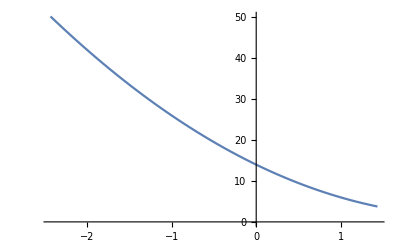

```mathematica
c1 = N[1/2 (-1-√15)];
c2 = N[1/2 (-1+√15)];
Plot[14-10 λ+2 λ^2, {λ, c1, c2}]
```

```mathematica
Sum[KroneckerDelta[i,j], {i, 61, 100}, {j, 1, 80}]
```

```mathematica
N@Log2[20/(√(40 80))]
ρ = 20/(√(40 80))
```

-1.5

1/(2 √2)

```mathematica
FullSimplify[√(40 80)√(1-ρ^2)]
```

20 √7

```mathematica
1/(2(1-ρ^2))
```

4/7

```mathematica
(2ρ)/(√(40 80))
```

1/80

```mathematica
s = "\\frac{1}{\\sqrt{2\\pi}^2 \\sigma_1 \\sigma_2 \\sqrt{1-\\rho^2}} \\exp\\left(
            - \\frac{1}{2(1-\\rho^2)} \\left[
                \\frac{(x_1-a_1)^2}{\\sigma_1^2} - \\rho \\frac{2 (x_1 - a_1)(x_2-a_2)}{\\sigma_1 \\sigma_2} + \\frac{(x_2-a_2)^2}{\\sigma_2^2}
            \\right]
        \\right)";
```

```mathematica
ClearAll[σ, x1, x2];
a1 = 0;
a2 = 0;
σ1 = √40 σ;
σ2 = √80 σ;
ρ = (20 σ^2)/(σ1 σ2);
```

```mathematica
FullSimplify[1/(2 π σ1 σ2 √(1-ρ^2)), σ>0]
```

1/(40 √7 π σ^2)

```mathematica
FullSimplify[-1/(2(1-ρ^2))((Y-a1)^2/σ1^2- ρ 2/(σ1 σ2)Y Z + Z^2/σ2^2)
, σ>0]
```

-(2 Y^2-Y Z+Z^2)/(140 σ^2)

```mathematica
e = 4.8 10^-10;
a = 10^-8 ;
r0 = 10^-13;
ScientificForm[e^2/a]
```

2.304×10^-11

```mathematica
ScientificForm[4./9(1/2) (r0/a)^2]
```

2.22222×10^-11

```mathematica
0.009 3 10^5
```

2700.